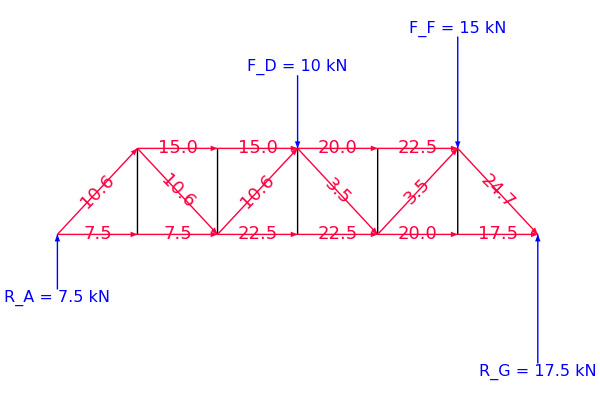

```mathematica
Module[{w,h,θ,FD,FF,sol,RG,RA,F2,F0,F7,F3,F5,F12,F8,F4,F10,F11,F13,F16,F15,F17,F19,F20,,colC,colT},
w=8;h=8;θ=ArcTan[h/w];FD=10;FF=15;

sol=Quiet@Solve[N@{
(*reactions*)
3*w*FD+5*w*FF-6*w*rg==0,
ra-FD-FF+rg==0,

(*cut 1*)
-f0*Sin[θ]+ra==0,
-f0*Cos[θ]+f2==0,

(*cut 2*)
-f7*Sin[θ]+ra==0,
-w*ra+h*f3==0,
f3-f5+f7*Cos[θ]==0,

(*cut 3*)
-f12*Sin[θ]+ra==0,
-2*w*ra+h*f8==0,
f4-f8-f12*Cos[θ]==0,

(*cut 4*)
f10*Sin[θ]+ra-FD==0,
-3*w*ra+h*f11==0,
-f10*Cos[θ]+f11-f13==0,

(*cut 5*)
f16*Sin[θ]+ra-FD==0,
-4*w*ra+w*FD+h*f17==0,
-f15+f16*Cos[θ]+f17==0,

(*cut 6*)
f19*Sin[θ]+ra-FD-FF==0,
-f19*Cos[θ]+f20==0

},{ra,rg,f0,f2,f3,f4,f5,f7,f8,f10,f11,f12,f13,f15,f16,f17,f19,f20}][[1]];
RG=rg/.sol;RA=ra/.sol;F0=f0/.sol;F2=f2/.sol;
F7=f7/.sol;F3=f3/.sol;
F5=f5/.sol;F12=f12/.sol;F8=f8/.sol;
F4=f4/.sol;F10=f10/.sol;F11=f11/.sol;
F13=f13/.sol;F16=f16/.sol;F15=f15/.sol;
F17=f17/.sol;F19=f19/.sol;F20=f20/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,
Line[{{#*w,0},{#*w,h}}]&/@Range@5,

{Blue,Arrow[{{3*w,1.85*h},{3*w,h}}],Arrow[{{5*w,2.3*h},{5*w,h}}],Text[Style[Row@{Subscript[Style["F",Italic],#2]," = ",#1," kN"},16],#3,{0,-1.5}]&@@@{{FD,"D",{3*w,1.85*h}},{FF,"F",{5*w,2.3*h}}},
Arrow[{{0,-0.64*h},{0,0}}],Arrow[{{6*w,-1.5*h},{6*w,0}}],Text[Style[Row@{Subscript[Style["R",Italic],#2]," = ",N@#1," kN"},16],#3,{0,1.5}]&@@@{{RA,"A",{0,-0.64*h}},{RG,"G",{6*w,-1.5*h}}}},

Flatten@{If[#1<0,{colC,Arrowheads@{-0.035,0.035}},{colT,Arrowheads@{{0.035,0.325},{-0.035,0.675}}}],#2,Text[Rotate[Style[NumberForm[Abs@#1,{3,1}],18,Background->White],#4],#3]}&@@@{
{F0,Arrow[{{0,0},{w,h}}],{w,h}/2,θ},{F2,Arrow[{{0,0},{w,0}}],{0.5*w,0},0},{F3,Arrow[{{w,0},{2*w,0}}],{1.5*w,0},0},{F4,Arrow[{{2*w,0},{3*w,0}}],{2.5*w,0},0},{F5,Arrow[{{w,h},{2*w,h}}],{1.5*w,h},0},{F7,Arrow[{{w,h},{2*w,0}}],{1.5*w,0.5*h},-θ},{F8,Arrow[{{2*w,h},{3*w,h}}],{2.5*w,h},0},{F10,Arrow[{{3*w,h},{4*w,0}}],{3.5*w,0.5*h},-θ},{F11,Arrow[{{3*w,0},{4*w,0}}],{3.5*w,0},0},{F12,Arrow[{{2*w,0},{3*w,h}}],{2.5*w,0.5*h},θ},{F13,Arrow[{{3*w,h},{4*w,h}}],{3.5*w,h},0},{F15,Arrow[{{4*w,h},{5*w,h}}],{4.5*w,h},0},{F16,Arrow[{{4*w,0},{5*w,h}}],{4.5*w,0.5*h},θ},{F17,Arrow[{{4*w,0},{5*w,0}}],{4.5*w,0},0},{F19,Arrow[{{5*w,h},{6*w,0}}],{5.5*w,0.5*h},-θ},{F20,Arrow[{{5*w,0},{6*w,0}}],{5.5*w,0},0}}
},ImageSize->{600,400}]
]
```

```mathematica
15+10.6*Cos[π/4]
```

22.4953

```mathematica
Module[{w,h,θ,FD,FF,sol,RG,RA,F2,F0,F7,F3,F5,F12,F8,F4,F10,F11,F13,F16,F15,F17,F19,F20,,colC,colT},
w=8;h=8;θ=ArcTan[h/w];FD=10;FF=15;

sol=Quiet@Solve[N@{
(*reactions*)3*w*FD+5*w*FF-6*w*rg==0,ra-FD-FF+rg==0,
(*cut 3*)-f12*Sin[θ]+ra==0,-2*w*ra+h*f8==0,f4-f8-f12*Cos[θ]==0
},{ra,rg,f4,f8,f12}]
]
```

{{ra→7.5,rg→17.5,f4→22.5,f8→15.,f12→10.6066}}